AngelRobots 
A set of 3 DoF robots engineered to be affordable in the poorest corners of the world

With reasonable trade-offs in precision relative to the intended application
With proposed applications in:
1. Wood working (CNC)
2. Agriculture
3. Metal working (CNC)
4. Construction (Brick laying)
5. Any other things that the creative mind can conceive.
6. Brick Making
7. Book Binding
8. Hospitality

Design Philosophy
-> It is a golden principle to “gather the fragments that nothing be lost, wasted”. It is also true that “the poor will be with us always”.  But by much economy much can be done in helping bring technological advance to the poorest corners of the world. This being our goal, our study and third-world engineering practice, goes beyond standard engineering to the study of standard parts, which due to mass production, are of low cost, and deeper still into which of a set of those that could perform the same mechanical function are the cheapest while not compromising on quality nor going below safety standards. Then designing robots to be built using these parts. The result is a set of robots that anyone can build and use, and as far as possible, everyone can afford, if not in person, then as a group.

## The Robots
1. 1 DoF (Frame)

```mathematica
motor[endPointofBarAgr_, barCrossSectionalWidth_,barCrossSectionalHeight_,  axis_, number_, axleDia_, bearingDia_, axleLength_, bearingLength_]:={
(*axleLength = 20;
bearingLength = 5;*)
endPointofBar= Switch[number, 0, endPointofBarAgr[[1]], 1, endPointofBarAgr[[2]]];
Switch[axis, "x",offsetX1=barCrossSectionalWidth/2;
offsetX1=barCrossSectionalWidth/2;
offsetX2= -barCrossSectionalWidth/2;
offsetX = Switch[number, 0,offsetX1, 1, offsetX2];
offsetY1=barCrossSectionalWidth/2;
offsetY2=-barCrossSectionalWidth/2;
offsetY = Switch[number, 0,offsetY1, 1, offsetY2];
offsetZ1=barCrossSectionalHeight;
offsetZ2= 0;
offsetZ = Switch[number, 0,offsetZ1, 1, offsetZ2],
"y",
offsetY1=0;
offsetY2=0;
];
axleAndBearingPoints = {
{
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ},
 {0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ+axleLength}
},
{
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ+axleLength-bearingLength},
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ+axleLength+25}
}
};
GraphicsGroup[{
Cylinder[axleAndBearingPoints[[1]], axleDia/2], Cylinder[axleAndBearingPoints[[2]], bearingDia/2]
}]

}

axleAndBearingPointsCalc[endPointofBarAgr_, barCrossSectionalWidth_,barCrossSectionalHeight_,  axis_, number_,axleDia_, bearingDia_, axleLength_, bearingLength_]:={
(*axleLength = 20;
bearingLength = 5;*)
endPointofBar= Switch[number, 0, endPointofBarAgr[[1]], 1, endPointofBarAgr[[2]]];
Switch[axis, "x",offsetX1=barCrossSectionalWidth/2;
offsetX1=barCrossSectionalWidth/2;
offsetX2= -barCrossSectionalWidth/2;
offsetX = Switch[number, 0,offsetX1, 1, offsetX2];
offsetY1=barCrossSectionalWidth/2;
offsetY2=-barCrossSectionalWidth/2;
offsetY = Switch[number, 0,offsetY1, 1, offsetY2];
offsetZ1=barCrossSectionalHeight;
offsetZ2= 0;
offsetZ = Switch[number, 0,offsetZ1, 1, offsetZ2],
"y",
offsetY1=0;
offsetY2=0;
];
axleAndBearingPoints = {
{
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ},
 {0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ+axleLength}
},
{
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ+axleLength-bearingLength},
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY,endPointofBar[[3]]+offsetZ+axleLength}
}
};
GraphicsGroup[{
Cylinder[axleAndBearingPoints[[1]],  axleDia/2], Cylinder[axleAndBearingPoints[[2]], bearingDia/2]
}]

}

chain[endPointofBarAgr_, barCrossSectionalWidth_,barCrossSectionalHeight_,  axis_, number_,axleDia_, bearingDia_, axleLength_, bearingLength_]:={
(*axleLength = 20;
bearingLength = 5;*)
endPointofBar= Switch[number, 0, endPointofBarAgr[[1]], 1, endPointofBarAgr[[2]]];
Switch[axis, "x",offsetX1=barCrossSectionalWidth/2;
offsetX1=barCrossSectionalWidth/2;
offsetX2= -barCrossSectionalWidth/2;
offsetX = Switch[number, 0,offsetX1, 1, offsetX2] -  barCrossSectionalWidth/2;
chainX = endPointofBarAgr[[2]][[1]]-endPointofBarAgr[[1]][[1]];
offsetY1=0;
chainY=0;
offsetY2=-barCrossSectionalWidth;
offsetY = Switch[number, 0,offsetY1, 1, offsetY2];
offsetZ1=barCrossSectionalHeight;
offsetZ2= 0;
offsetZ = Switch[number, 0,offsetZ1, 1, offsetZ2],
"y",
offsetY1=0;
offsetY2=0;
];
chainPoints = 
{
{0+endPointofBar[[1]]+offsetX,0+endPointofBar[[2]]+offsetY+chainY,endPointofBar[[3]]+offsetZ+axleLength},
 {0+endPointofBar[[1]]+offsetX+ chainX,0+endPointofBar[[2]]+offsetY+chainY,endPointofBar[[3]]+offsetZ+axleLength}
};
GraphicsGroup[{
Thick, Line[chainPoints]
}]

}



(*along x*)
halfWorkSpaceWidth = 700; 
OneDoFFrame[x_,y_, z_, offsetX_, offsetY_, offsetZ_]:=Module[{},{
origin = {0,0,0};
outerCylinderHeight=210;
minCylinderHeight=270;
maxCylinderLength = 460;
maxDisp  = maxCylinderLength-minCylinderHeight;
barCrossSectionalWidth = 51; (*2 inches*)
barCrossSectionalHeight = 51;
axleDia =5;
bearingDia = 10;
axleLength=10;
bearingLengh=5;
motorLength=15;
outerCylinderDia= 47;
innerCylinderDia = 38.5;
addedOrigin = 0;
(*Workspace*)
halfWorkSpaceLength = minCylinderHeight+ maxDisp + 2*barCrossSectionalWidth; (*along Y*)(*5*barCrossSectionalWidth+maxCylinderLength;*)
(*firstHalf*)
frameOrigin = {origin[[1]] + offsetX,origin[[2]] + offsetY, origin[[3]] + offsetZ};
firstFrameBar1Points = {
{frameOrigin[[1]], frameOrigin[[2]],frameOrigin[[3]]},
{frameOrigin[[1]]+halfWorkSpaceWidth + 2 * barCrossSectionalWidth, frameOrigin[[2]]+barCrossSectionalWidth,frameOrigin[[3]]+barCrossSectionalHeight}
};
(*counter clockwise*)
firstFrameBar2Points = {
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth+barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength, firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar3Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[2]][[3]]}
};
firstFrameBar4Points = {
{firstFrameBar2Points[[1]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[1]][[2]], firstFrameBar2Points[[1]][[3]]},
{firstFrameBar2Points[[2]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[2]][[2]], firstFrameBar2Points[[2]][[3]]}
};
firstFrameBar5Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]], firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar6Points = {
{firstFrameBar5Points[[1]][[1]], firstFrameBar5Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[1]][[3]]},
{firstFrameBar5Points[[2]][[1]], firstFrameBar5Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[2]][[3]]}
};
firstFrameOuterCylinder1Points = {
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight},
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+outerCylinderHeight, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight}
};
firstFrameOuterCylinder2Points = {
{firstFrameOuterCylinder1Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[1]][[2]], firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[2]][[2]], firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder1Points = {
{firstFrameOuterCylinder1Points[[1]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y, firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder2Points = {
{firstFrameOuterCylinder2Points[[1]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y, firstFrameOuterCylinder2Points[[1]][[3]]},
{firstFrameOuterCylinder2Points[[2]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder2Points[[2]][[3]]}
};
firstFrameBar7Points = {
{firstFrameBar6Points[[1]][[1]], firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[1]][[3]]},
{firstFrameBar6Points[[2]][[1]], firstFrameBar6Points[[2]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[2]][[3]]}
};
firstFrameBar8Points = {
{firstFrameBar3Points[[1]][[1]], firstFrameBar3Points[[1]][[2]], firstFrameBar3Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar3Points[[2]][[1]], firstFrameBar3Points[[2]][[2]], firstFrameBar3Points[[2]][[3]]+barCrossSectionalHeight}
};
(*
axle1= axleAndBearingPointsCalc[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
axle2= axleAndBearingPointsCalc[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
axle3= axleAndBearingPointsCalc[firstFrameBar8Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
axle4= motor[firstFrameBar8Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, motorLength];
axle5= axleAndBearingPointsCalc[firstFrameBar7Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
axle6= axleAndBearingPointsCalc[firstFrameBar7Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
chain1 = chain[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
*)
{
Cuboid[firstFrameBar1Points[[1]],firstFrameBar1Points[[2]]]
,
Cuboid[firstFrameBar2Points[[1]],firstFrameBar2Points[[2]]],
Cuboid[firstFrameBar3Points[[1]],firstFrameBar3Points[[2]]],
Cuboid[firstFrameBar4Points[[1]],firstFrameBar4Points[[2]]],
Cuboid[firstFrameBar5Points[[1]],firstFrameBar5Points[[2]]],
Cuboid[firstFrameBar6Points[[1]],firstFrameBar6Points[[2]]],
Cylinder[firstFrameOuterCylinder1Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder2Points, outerCylinderDia/2],
Cyan,
Cylinder[firstFrameInnerCylinder1Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder2Points, innerCylinderDia/2],
Cuboid[firstFrameBar7Points[[1]],firstFrameBar7Points[[2]]],
Orange,
Cuboid[firstFrameBar8Points[[1]],firstFrameBar8Points[[2]]]
(*axle1,axle2, axle3, axle4, axle5, axle6,
chain1*)
}
}]
OneDoFFramewithGantry[x_,y_, z_, offsetX_, offsetY_, offsetZ_]:=Module[{},{
origin = {0,0,0};
(*halfWorkSpaceWidth = 100;*) (*along x*)
outerCylinderHeight=210;
minCylinderHeight=270;
maxCylinderLength = 460;
maxDisp  = maxCylinderLength-minCylinderHeight;
barCrossSectionalWidth = 51; (*2 inches*)
barCrossSectionalHeight = 51;
axleDia =5;
bearingDia = 10;
axleLength=10;
bearingLengh=5;
motorLength=15;
outerCylinderDia= 47;
innerCylinderDia = 38.5;
addedOrigin = 0;
(*Workspace*)
halfWorkSpaceLength = minCylinderHeight+ maxDisp + 2*barCrossSectionalWidth; (*along Y*)(*5*barCrossSectionalWidth+maxCylinderLength;*)
(*firstHalf*)
frameOrigin = {origin[[1]] + offsetX,origin[[2]] + offsetY, origin[[3]] + offsetZ};
firstFrameBar1Points = {
{frameOrigin[[1]], frameOrigin[[2]],frameOrigin[[3]]},
{frameOrigin[[1]]+halfWorkSpaceWidth + 2 * barCrossSectionalWidth, frameOrigin[[2]]+barCrossSectionalWidth,frameOrigin[[3]]+barCrossSectionalHeight}
};
(*counter clockwise*)
firstFrameBar2Points = {
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth+barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength, firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar3Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[2]][[3]]}
};
firstFrameBar4Points = {
{firstFrameBar2Points[[1]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[1]][[2]], firstFrameBar2Points[[1]][[3]]},
{firstFrameBar2Points[[2]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[2]][[2]], firstFrameBar2Points[[2]][[3]]}
};
firstFrameBar5Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]], firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar6Points = {
{firstFrameBar5Points[[1]][[1]], firstFrameBar5Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[1]][[3]]},
{firstFrameBar5Points[[2]][[1]], firstFrameBar5Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[2]][[3]]}
};
firstFrameOuterCylinder1Points = {
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight},
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+outerCylinderHeight, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight}
};
firstFrameOuterCylinder2Points = {
{firstFrameOuterCylinder1Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[1]][[2]], firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[2]][[2]], firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder1Points = {
{firstFrameOuterCylinder1Points[[1]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y, firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder2Points = {
{firstFrameOuterCylinder2Points[[1]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y, firstFrameOuterCylinder2Points[[1]][[3]]},
{firstFrameOuterCylinder2Points[[2]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder2Points[[2]][[3]]}
};
firstFrameBar7Points = {
{firstFrameBar6Points[[1]][[1]], firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[1]][[3]]},
{firstFrameBar6Points[[1]][[1]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+300}
};
firstFrameBar9Points = {
{firstFrameBar7Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar7Points[[1]][[2]], firstFrameBar7Points[[1]][[3]]},
{firstFrameBar7Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar7Points[[2]][[2]], firstFrameBar7Points[[2]][[3]]}
};
firstFrameBar10Points = {
{firstFrameBar7Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar7Points[[2]][[2]]-barCrossSectionalWidth, firstFrameBar7Points[[2]][[3]]},
{firstFrameBar9Points[[2]][[1]], firstFrameBar9Points[[2]][[2]], firstFrameBar9Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar8Points = {
{firstFrameBar3Points[[1]][[1]], firstFrameBar3Points[[1]][[2]], firstFrameBar3Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar3Points[[2]][[1]], firstFrameBar3Points[[2]][[2]], firstFrameBar3Points[[2]][[3]]+barCrossSectionalHeight}
};
(*
axle1= axleAndBearingPointsCalc[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
axle2= axleAndBearingPointsCalc[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
axle3= axleAndBearingPointsCalc[firstFrameBar8Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
axle4= motor[firstFrameBar8Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, motorLength];
axle5= axleAndBearingPointsCalc[firstFrameBar7Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
axle6= axleAndBearingPointsCalc[firstFrameBar7Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
chain1 = chain[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
*)
{
Cuboid[firstFrameBar1Points[[1]],firstFrameBar1Points[[2]]]
,
Cuboid[firstFrameBar2Points[[1]],firstFrameBar2Points[[2]]],
Cuboid[firstFrameBar3Points[[1]],firstFrameBar3Points[[2]]],
Cuboid[firstFrameBar4Points[[1]],firstFrameBar4Points[[2]]],
Cuboid[firstFrameBar5Points[[1]],firstFrameBar5Points[[2]]],
Cuboid[firstFrameBar6Points[[1]],firstFrameBar6Points[[2]]],
Cylinder[firstFrameOuterCylinder1Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder2Points, outerCylinderDia/2],
Cyan,
Cylinder[firstFrameInnerCylinder1Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder2Points, innerCylinderDia/2],
Cuboid[firstFrameBar7Points[[1]],firstFrameBar7Points[[2]]],
Cuboid[firstFrameBar9Points[[1]],firstFrameBar9Points[[2]]],
Cuboid[firstFrameBar10Points[[1]],firstFrameBar10Points[[2]]],
Orange,
Cuboid[firstFrameBar8Points[[1]],firstFrameBar8Points[[2]]]
}
}]
OneDoFDoubleFrame[x_,y_, z_, offsetX_, offsetY_, offsetZ_]:=Module[{},{
origin = {0,0,0};
outerCylinderHeight=210;
minCylinderHeight=270;
maxCylinderLength = 460;
maxDisp  = maxCylinderLength-minCylinderHeight;
barCrossSectionalWidth = 51; (*2 inches*)
barCrossSectionalHeight = 51;
axleDia =5;
bearingDia = 10;
axleLength=10;
bearingLengh=5;
motorLength=15;
outerCylinderDia= 47;
innerCylinderDia = 38.5;
addedOrigin = 0;
(*Workspace*)
halfWorkSpaceLength = minCylinderHeight+ maxDisp + 2*barCrossSectionalWidth; (*along Y*)(*5*barCrossSectionalWidth+maxCylinderLength;*)
(*firstHalf*)
frameOrigin = {origin[[1]] + offsetX,origin[[2]] + offsetY, origin[[3]] + offsetZ};
firstFrameBar1Points = {
{frameOrigin[[1]], frameOrigin[[2]],frameOrigin[[3]]},
{frameOrigin[[1]]+halfWorkSpaceWidth + 2 * barCrossSectionalWidth, frameOrigin[[2]]+barCrossSectionalWidth,frameOrigin[[3]]+barCrossSectionalHeight}
};
(*counter clockwise*)
firstFrameBar2Points = {
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth+barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength, firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar3Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[2]][[3]]}
};
firstFrameBar4Points = {
{firstFrameBar2Points[[1]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[1]][[2]], firstFrameBar2Points[[1]][[3]]},
{firstFrameBar2Points[[2]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[2]][[2]], firstFrameBar2Points[[2]][[3]]}
};
firstFrameBar5Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]], firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar6Points = {
{firstFrameBar5Points[[1]][[1]], firstFrameBar5Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[1]][[3]]},
{firstFrameBar5Points[[2]][[1]], firstFrameBar5Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[2]][[3]]}
};
firstFrameOuterCylinder1Points = {
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight},
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+outerCylinderHeight, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight}
};
firstFrameOuterCylinder2Points = {
{firstFrameOuterCylinder1Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[1]][[2]], firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[2]][[2]], firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder1Points = {
{firstFrameOuterCylinder1Points[[1]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y, firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder2Points = {
{firstFrameOuterCylinder2Points[[1]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y, firstFrameOuterCylinder2Points[[1]][[3]]},
{firstFrameOuterCylinder2Points[[2]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder2Points[[2]][[3]]}
};
firstFrameBar7Points = {
{firstFrameBar6Points[[1]][[1]], firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[1]][[3]]},
{firstFrameBar6Points[[2]][[1]], firstFrameBar6Points[[2]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[2]][[3]]}
};
(*firstFrameBar8Points = {
{firstFrameBar3Points[[1]][[1]], firstFrameBar3Points[[1]][[2]], firstFrameBar3Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar3Points[[2]][[1]], firstFrameBar3Points[[2]][[2]], firstFrameBar3Points[[2]][[3]]+barCrossSectionalHeight}
};*)
firstFrameBar8Points = {
{firstFrameBar7Points[[1]][[1]], firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[3]]},
{firstFrameBar7Points[[1]][[1]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth+halfWorkSpaceLength, firstFrameBar7Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar9Points = {
{firstFrameBar8Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[1]][[2]], firstFrameBar8Points[[1]][[3]]},
{firstFrameBar8Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]}
};
firstFrameBar10Points = {
{firstFrameBar8Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]-barCrossSectionalHeight},
{firstFrameBar9Points[[2]][[1]], firstFrameBar9Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar9Points[[2]][[3]]}
};
firstFrameBar11Points = {
{firstFrameBar10Points[[1]][[1]], firstFrameBar10Points[[1]][[2]], firstFrameBar10Points[[1]][[3]]-barCrossSectionalHeight},
{firstFrameBar10Points[[2]][[1]], firstFrameBar10Points[[2]][[2]], firstFrameBar10Points[[2]][[3]]-barCrossSectionalHeight}
};
firstFrameBar12Points = {
{firstFrameBar11Points[[1]][[1]], firstFrameBar11Points[[1]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[1]][[3]]},
{firstFrameBar11Points[[2]][[1]], firstFrameBar11Points[[2]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[2]][[3]]}
};
firstFrameOuterCylinder3Points = {
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]], firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2},
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]]-outerCylinderHeight, firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2}
};(*check 200*)
firstFrameOuterCylinder4Points = {
{firstFrameOuterCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[1]][[2]], firstFrameOuterCylinder3Points[[1]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]] +halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[2]][[2]], firstFrameOuterCylinder3Points[[2]][[3]]}
};
(*inverseY = maxDisp-y;*)
firstFrameInnerCylinder3Points = {
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y, firstFrameOuterCylinder3Points[[2]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y-minCylinderHeight, firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder4Points = {
{firstFrameInnerCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[1]][[2]], firstFrameInnerCylinder3Points[[1]][[3]]},
{firstFrameInnerCylinder3Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[2]][[2]], firstFrameInnerCylinder3Points[[2]][[3]]}
};
(*
axle1= axleAndBearingPointsCalc[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
axle2= axleAndBearingPointsCalc[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
axle3= axleAndBearingPointsCalc[firstFrameBar8Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
axle4= motor[firstFrameBar8Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, motorLength];
axle5= axleAndBearingPointsCalc[firstFrameBar7Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
axle6= axleAndBearingPointsCalc[firstFrameBar7Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 1, axleDia, bearingDia, axleLength, bearingLength];
chain1 = chain[firstFrameBar6Points, barCrossSectionalWidth,barCrossSectionalHeight,  "x", 0, axleDia, bearingDia, axleLength, bearingLength];
*)
{
Cuboid[firstFrameBar1Points[[1]],firstFrameBar1Points[[2]]]
,
Cuboid[firstFrameBar2Points[[1]],firstFrameBar2Points[[2]]],
Cuboid[firstFrameBar3Points[[1]],firstFrameBar3Points[[2]]],
Cuboid[firstFrameBar4Points[[1]],firstFrameBar4Points[[2]]],
Cuboid[firstFrameBar5Points[[1]],firstFrameBar5Points[[2]]],
Cuboid[firstFrameBar6Points[[1]],firstFrameBar6Points[[2]]],
Cylinder[firstFrameOuterCylinder1Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder2Points, outerCylinderDia/2],
Cyan,
Cylinder[firstFrameInnerCylinder1Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder2Points, innerCylinderDia/2],
Cuboid[firstFrameBar7Points[[1]],firstFrameBar7Points[[2]]],
Orange,
Cuboid[firstFrameBar8Points[[1]],firstFrameBar8Points[[2]]],
Cuboid[firstFrameBar9Points[[1]],firstFrameBar9Points[[2]]],
Cuboid[firstFrameBar10Points[[1]],firstFrameBar10Points[[2]]],
Cuboid[firstFrameBar11Points[[1]],firstFrameBar11Points[[2]]],
Cuboid[firstFrameBar12Points[[1]],firstFrameBar12Points[[2]]],
Cyan,
Cylinder[firstFrameOuterCylinder3Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder4Points, outerCylinderDia/2],Pink,
Cylinder[firstFrameInnerCylinder3Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder4Points, innerCylinderDia/2]

(*axle1,axle2, axle3, axle4, axle5, axle6,
chain1*)
}
}]
OneDoFDoubleFrameMobile[x_,ySystem_, z_, offsetX_, offsetY_, offsetZ_, len_]:=Module[{},{


outerCylinderHeight=210;
minCylinderHeight=270;
maxCylinderLength = 460;
maxDisp  = maxCylinderLength-minCylinderHeight;

offsetYBar1 = Floor[(Floor[ySystem,(maxDisp*2)]*(maxDisp*2))/(maxDisp*2)] /2 ;
offsetYBarNext = Floor[(Ceiling[ySystem,(maxDisp*2)]*(maxDisp*2))/(maxDisp*2)] /2 ;
(*y = ySystem - offsetYBar1;*)
internalY = Mod[ySystem,maxDisp];
realBarOffsetY=Switch[Mod[Floor[ySystem/(maxDisp)],2]== 1,True, offsetYBarNext-(maxDisp-internalY),False, offsetYBar1];
origin = {0,realBarOffsetY,0};
y = Switch[Mod[Floor[ySystem/(maxDisp)],2]== 1,True, maxDisp-internalY,False, internalY];
barCrossSectionalWidth = 51;
barCrossSectionalHeight = 51;
axleDia =5;
bearingDia = 10;
axleLength=10;
bearingLengh=5;
motorLength=15;
outerCylinderDia= 47;
innerCylinderDia = 38.5;
addedOrigin = 0;

halfWorkSpaceLength = minCylinderHeight+ maxDisp + 2*barCrossSectionalWidth; 

frameOrigin = {origin[[1]] + offsetX,origin[[2]] + offsetY, origin[[3]] + offsetZ};
firstFrameBar1Points = {
{frameOrigin[[1]], frameOrigin[[2]],frameOrigin[[3]]},
{frameOrigin[[1]]+halfWorkSpaceWidth + 2 * barCrossSectionalWidth, frameOrigin[[2]]+barCrossSectionalWidth,frameOrigin[[3]]+barCrossSectionalHeight}
};

firstFrameBar2Points = {
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth+barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength, firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar3Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[2]][[3]]}
};
firstFrameBar4Points = {
{firstFrameBar2Points[[1]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[1]][[2]], firstFrameBar2Points[[1]][[3]]},
{firstFrameBar2Points[[2]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[2]][[2]], firstFrameBar2Points[[2]][[3]]}
};
firstFrameBar5Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]], firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar6Points = {
{firstFrameBar5Points[[1]][[1]], firstFrameBar5Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[1]][[3]]},
{firstFrameBar5Points[[2]][[1]], firstFrameBar5Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[2]][[3]]}
};
firstFrameOuterCylinder1Points = {
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight},
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+outerCylinderHeight, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight}
};
firstFrameOuterCylinder2Points = {
{firstFrameOuterCylinder1Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[1]][[2]], firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[2]][[2]], firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder1Points = {
{firstFrameOuterCylinder1Points[[1]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y, firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder2Points = {
{firstFrameOuterCylinder2Points[[1]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y, firstFrameOuterCylinder2Points[[1]][[3]]},
{firstFrameOuterCylinder2Points[[2]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder2Points[[2]][[3]]}
};
firstFrameBar7Points = {
{firstFrameBar6Points[[1]][[1]], firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[1]][[3]]},
{firstFrameBar6Points[[2]][[1]], firstFrameBar6Points[[2]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[2]][[3]]}
};
firstFrameBar8Points = {
{firstFrameBar7Points[[1]][[1]], firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[3]]},
{firstFrameBar7Points[[1]][[1]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth+halfWorkSpaceLength, firstFrameBar7Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar9Points = {
{firstFrameBar8Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[1]][[2]], firstFrameBar8Points[[1]][[3]]},
{firstFrameBar8Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]}
};
firstFrameBar10Points = {
{firstFrameBar8Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]-barCrossSectionalHeight},
{firstFrameBar9Points[[2]][[1]], firstFrameBar9Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar9Points[[2]][[3]]}
};
firstFrameBar11Points = {
{firstFrameBar10Points[[1]][[1]], firstFrameBar10Points[[1]][[2]], firstFrameBar10Points[[1]][[3]]-barCrossSectionalHeight},
{firstFrameBar10Points[[2]][[1]], firstFrameBar10Points[[2]][[2]], firstFrameBar10Points[[2]][[3]]-barCrossSectionalHeight}
};
firstFrameBar12Points = {
{firstFrameBar11Points[[1]][[1]], firstFrameBar11Points[[1]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[1]][[3]]},
{firstFrameBar11Points[[2]][[1]], firstFrameBar11Points[[2]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[2]][[3]]}
};
firstFrameOuterCylinder3Points = {
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]], firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2},
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]]-outerCylinderHeight, firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2}
};
firstFrameOuterCylinder4Points = {
{firstFrameOuterCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[1]][[2]], firstFrameOuterCylinder3Points[[1]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]] +halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[2]][[2]], firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder3Points = {
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y, firstFrameOuterCylinder3Points[[2]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y-minCylinderHeight, firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder4Points = {
{firstFrameInnerCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[1]][[2]], firstFrameInnerCylinder3Points[[1]][[3]]},
{firstFrameInnerCylinder3Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[2]][[2]], firstFrameInnerCylinder3Points[[2]][[3]]}
};

{
Line[{{0,0,0}, {0, (Ceiling[len/(maxDisp*2)])*maxDisp+ 4*barCrossSectionalWidth+minCylinderHeight+halfWorkSpaceLength -
Switch[Mod[len, (maxDisp*2)]==0,True,0,False,
(maxDisp-Mod[len, (maxDisp*2)])]
,0}}],
Cuboid[firstFrameBar1Points[[1]],firstFrameBar1Points[[2]]]
,
Cuboid[firstFrameBar2Points[[1]],firstFrameBar2Points[[2]]],
Cuboid[firstFrameBar3Points[[1]],firstFrameBar3Points[[2]]],
Cuboid[firstFrameBar4Points[[1]],firstFrameBar4Points[[2]]],
Cuboid[firstFrameBar5Points[[1]],firstFrameBar5Points[[2]]],
Cuboid[firstFrameBar6Points[[1]],firstFrameBar6Points[[2]]],
Cylinder[firstFrameOuterCylinder1Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder2Points, outerCylinderDia/2],
Cyan,
Cylinder[firstFrameInnerCylinder1Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder2Points, innerCylinderDia/2],
Cuboid[firstFrameBar7Points[[1]],firstFrameBar7Points[[2]]],
Orange,
Cuboid[firstFrameBar8Points[[1]],firstFrameBar8Points[[2]]],
Cuboid[firstFrameBar9Points[[1]],firstFrameBar9Points[[2]]],
Cuboid[firstFrameBar10Points[[1]],firstFrameBar10Points[[2]]],
Cuboid[firstFrameBar11Points[[1]],firstFrameBar11Points[[2]]],
Cuboid[firstFrameBar12Points[[1]],firstFrameBar12Points[[2]]],
Cyan,
Cylinder[firstFrameOuterCylinder3Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder4Points, outerCylinderDia/2],Pink,
Cylinder[firstFrameInnerCylinder3Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder4Points, innerCylinderDia/2]
},
firstFrameBar3Points[[1]][[2]],
firstFrameBar7Points[[1]][[2]],
(firstFrameBar3Points[[1]][[2]]+firstFrameBar7Points[[1]][[2]])/2
}]
(*
Plot[{ OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[1]],OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[2]]}, {ys,0,1200}]
Plot[{ OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[2]], OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[5]],  OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[4]]}, {ys,0,1200}]
Plot[{OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[1]], OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[2]], OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[3]], OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[4]],OneDoFDoubleFrameMobile[0,ys,0,0,0,0][[5]]}, {ys,0,1200}]
*)

(*OneDoFDoubleFrameMobile[0,y1,0,0,0,0, WorkSpaceLength][[3]]*)
(*Plot[{OneDoFDoubleFrameMobile[0,ye1,0,0,0,0, WorkSpaceLength][[2]]}, {ye1,380,WorkSpaceLength}]*)
(**)
(*OneDoFFrame[0,0,0, 0,0,0]*)
(*Graphics3D[OneDoFFrame[0,0,0,0,0,0], Axes-> True, AxesLabel->{"X","Y", "Z"}]*)

TwoDoFDoubleFrameMobile[x_,ySystem_, z_, offsetX_, offsetY_, offsetZ_, len_(*along y*), wid_ (*along x*)]:=Module[{},{
outerCylinderHeight=210;
minCylinderHeight=270;
maxCylinderLength = 460;
maxDisp  = maxCylinderLength-minCylinderHeight;

offsetYBar1 = Floor[(Floor[ySystem,(maxDisp*2)]*(maxDisp*2))/(maxDisp*2)] /2 ;
offsetYBarNext = Floor[(Ceiling[ySystem,(maxDisp*2)]*(maxDisp*2))/(maxDisp*2)] /2 ;
(*y = ySystem - offsetYBar1;*)
internalY = Mod[ySystem,maxDisp];
realBarOffsetY=Switch[Mod[Floor[ySystem/(maxDisp)],2]== 1,True, offsetYBarNext-(maxDisp-internalY),False, offsetYBar1];
origin = {0,realBarOffsetY,0};
y = Switch[Mod[Floor[ySystem/(maxDisp)],2]== 1,True, maxDisp-internalY,False, internalY];
barCrossSectionalWidth = 51;
barCrossSectionalHeight = 51;
axleDia =5;
bearingDia = 10;
axleLength=10;
bearingLengh=5;
motorLength=15;
outerCylinderDia= 47;
innerCylinderDia = 38.5;
addedOrigin = 0;

halfWorkSpaceLength = minCylinderHeight+ maxDisp + 2*barCrossSectionalWidth; 
halfWorkSpaceWidth = wid;

frameOrigin = {origin[[1]] + offsetX,origin[[2]] + offsetY, origin[[3]] + offsetZ};
firstFrameBar1Points = {
{frameOrigin[[1]], frameOrigin[[2]],frameOrigin[[3]]},
{frameOrigin[[1]]+halfWorkSpaceWidth + 2 * barCrossSectionalWidth, frameOrigin[[2]]+barCrossSectionalWidth,frameOrigin[[3]]+barCrossSectionalHeight}
};

firstFrameBar2Points = {
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth+barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength, firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar3Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[2]][[3]]}
};
firstFrameBar4Points = {
{firstFrameBar2Points[[1]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[1]][[2]], firstFrameBar2Points[[1]][[3]]},
{firstFrameBar2Points[[2]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[2]][[2]], firstFrameBar2Points[[2]][[3]]}
};
firstFrameBar5Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]], firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar6Points = {
{firstFrameBar5Points[[1]][[1]], firstFrameBar5Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[1]][[3]]},
{firstFrameBar5Points[[2]][[1]], firstFrameBar5Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[2]][[3]]}
};
firstFrameOuterCylinder1Points = {
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight},
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+outerCylinderHeight, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight}
};
firstFrameOuterCylinder2Points = {
{firstFrameOuterCylinder1Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[1]][[2]], firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[2]][[2]], firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder1Points = {
{firstFrameOuterCylinder1Points[[1]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y, firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder2Points = {
{firstFrameOuterCylinder2Points[[1]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y, firstFrameOuterCylinder2Points[[1]][[3]]},
{firstFrameOuterCylinder2Points[[2]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder2Points[[2]][[3]]}
};
firstFrameBar7Points = {
{firstFrameBar6Points[[1]][[1]], firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[1]][[3]]},
{firstFrameBar6Points[[2]][[1]], firstFrameBar6Points[[2]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[2]][[3]]}
};
firstFrameBar8Points = {
{firstFrameBar7Points[[1]][[1]], firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[3]]},
{firstFrameBar7Points[[1]][[1]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth+halfWorkSpaceLength, firstFrameBar7Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar9Points = {
{firstFrameBar8Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[1]][[2]], firstFrameBar8Points[[1]][[3]]},
{firstFrameBar8Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]}
};
firstFrameBar10Points = {
{firstFrameBar8Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]-barCrossSectionalHeight},
{firstFrameBar9Points[[2]][[1]], firstFrameBar9Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar9Points[[2]][[3]]}
};
firstFrameBar11Points = {
{firstFrameBar10Points[[1]][[1]], firstFrameBar10Points[[1]][[2]], firstFrameBar10Points[[1]][[3]]-barCrossSectionalHeight},
{firstFrameBar10Points[[2]][[1]], firstFrameBar10Points[[2]][[2]], firstFrameBar10Points[[2]][[3]]-barCrossSectionalHeight}
};
firstFrameBar12Points = {
{firstFrameBar11Points[[1]][[1]], firstFrameBar11Points[[1]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[1]][[3]]},
{firstFrameBar11Points[[2]][[1]], firstFrameBar11Points[[2]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[2]][[3]]}
};
firstFrameOuterCylinder3Points = {
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]], firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2},
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]]-outerCylinderHeight, firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2}
};
firstFrameOuterCylinder4Points = {
{firstFrameOuterCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[1]][[2]], firstFrameOuterCylinder3Points[[1]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]] +halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[2]][[2]], firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder3Points = {
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y, firstFrameOuterCylinder3Points[[2]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y-minCylinderHeight, firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder4Points = {
{firstFrameInnerCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[1]][[2]], firstFrameInnerCylinder3Points[[1]][[3]]},
{firstFrameInnerCylinder3Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[2]][[2]], firstFrameInnerCylinder3Points[[2]][[3]]}
};

{
Line[{{0,0,0}, {0, (Ceiling[len/(maxDisp*2)])*maxDisp+ 4*barCrossSectionalWidth+minCylinderHeight+halfWorkSpaceLength -
Switch[Mod[len, (maxDisp*2)]==0,True,0,False,
(maxDisp-Mod[len, (maxDisp*2)])]
,0}}],
Cuboid[firstFrameBar1Points[[1]],firstFrameBar1Points[[2]]]
,
Cuboid[firstFrameBar2Points[[1]],firstFrameBar2Points[[2]]],
(*Cuboid[firstFrameBar3Points[[1]],firstFrameBar3Points[[2]]],*)(*Remove because it will be an obstruction to x-axis*)
Cuboid[firstFrameBar4Points[[1]],firstFrameBar4Points[[2]]],
Cuboid[firstFrameBar5Points[[1]],firstFrameBar5Points[[2]]],
Cuboid[firstFrameBar6Points[[1]],firstFrameBar6Points[[2]]],
Cylinder[firstFrameOuterCylinder1Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder2Points, outerCylinderDia/2],
Cyan,
Cylinder[firstFrameInnerCylinder1Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder2Points, innerCylinderDia/2],
Cuboid[firstFrameBar7Points[[1]],firstFrameBar7Points[[2]]],
Orange,
Cuboid[firstFrameBar8Points[[1]],firstFrameBar8Points[[2]]],
Cuboid[firstFrameBar9Points[[1]],firstFrameBar9Points[[2]]],
Cuboid[firstFrameBar10Points[[1]],firstFrameBar10Points[[2]]],
Cuboid[firstFrameBar11Points[[1]],firstFrameBar11Points[[2]]],
Cuboid[firstFrameBar12Points[[1]],firstFrameBar12Points[[2]]],
Cyan,
Cylinder[firstFrameOuterCylinder3Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder4Points, outerCylinderDia/2],Pink,
Cylinder[firstFrameInnerCylinder3Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder4Points, innerCylinderDia/2]
},
firstFrameBar3Points[[1]][[2]],
firstFrameBar7Points[[1]][[2]],
(firstFrameBar3Points[[1]][[2]]+firstFrameBar7Points[[1]][[2]])/2
}]
OneDoFCabledFrameContinuousMotion[yArg_,frameLength_, frameWidth_, yMin_, yMaxArg_]:=Module[{},{
(*Motion alonog y*)
barCrossSectionalWidth = 51; (*2 inches*)
barCrossSectionalHeight = 51;
axleLength = 2.5*barCrossSectionalHeight;
bearingLength = 2*barCrossSectionalHeight;
axleDia = 0.25*barCrossSectionalWidth;
bearingDia = 2*barCrossSectionalWidth;
ropeDia = 0.25*barCrossSectionalWidth;
bar1xStart = 0 ;bar1xEnd =   frameWidth/1 ;
Switch[yArg > yMaxArg,True, ys=yMaxArg, False, ys=yArg];
bar1yStart = -frameLength/2-barCrossSectionalWidth;bar1yEnd=bar1yStart+barCrossSectionalWidth;
bar1zStart = 0;bar1zEnd = barCrossSectionalHeight;
bar1Points = {{bar1xStart,bar1yStart, bar1zStart },{bar1xEnd, bar1yEnd, bar1zEnd}};

bar2xStart = bar1xEnd - barCrossSectionalWidth;
bar2xEnd = bar2xStart+barCrossSectionalWidth;
bar2yStart = bar1yEnd;
bar2yEnd  = bar2yStart +frameLength;
bar2zStart = bar1zStart;
bar2zEnd = bar1zEnd;
bar2Points={{bar2xStart,bar2yStart,bar2zStart},{bar2xEnd,bar2yEnd,bar2zEnd}};

bar3xStart=bar1xStart;
bar3xEnd=bar1xEnd;
bar3yStart=bar2yEnd;(*bar1yStart+frameLength;*)
bar3yEnd=bar3yStart+barCrossSectionalWidth;
bar3zStart=bar1zStart;
bar3zEnd=bar1zEnd;
bar3Points={{bar3xStart,bar3yStart,bar3zStart},{bar3xEnd,bar3yEnd,bar3zEnd}};

bar4xStart=bar2xStart-frameWidth+barCrossSectionalWidth;
bar4xEnd=bar4xStart+barCrossSectionalWidth;
bar4yStart=bar2yStart;
bar4yEnd=bar2yEnd;
bar4zStart=bar2zStart;
bar4zEnd=bar2zEnd;
bar4Points={{bar4xStart,bar4yStart,bar4zStart},{bar4xEnd,bar4yEnd,bar4zEnd}};

bar5xStart=bar1xStart;
bar5xEnd=bar1xEnd;
bar5yStart=0-yMin-barCrossSectionalWidth-ys;
bar5yEnd=bar5yStart+barCrossSectionalWidth;
bar5zStart=barCrossSectionalHeight;
bar5zEnd=barCrossSectionalHeight+barCrossSectionalHeight;
bar5Points={{bar5xStart,bar5yStart,bar5zStart},{bar5xEnd,bar5yEnd,bar5zEnd}};


bar6xStart=bar1xStart;
bar6xEnd=bar1xEnd;
bar6yStart=0+yMin+ys;
bar6yEnd=bar6yStart+barCrossSectionalWidth;
bar6zStart=barCrossSectionalHeight;
bar6zEnd=barCrossSectionalHeight+barCrossSectionalHeight;
bar6Points={{bar6xStart,bar6yStart,bar6zStart},{bar6xEnd,bar6yEnd,bar6zEnd}};
axle1xStart = bar1xStart + frameWidth/2;axle1xEnd = axle1xStart;
axle1yStart = bar1yStart + barCrossSectionalWidth/2;axle1yEnd = axle1yStart;
axle1zStart = bar1zEnd;axle1zEnd = axle1zStart+axleLength;
axle1Points={{axle1xStart,axle1yStart,axle1zStart},{axle1xEnd,axle1yEnd,axle1zEnd}};
axle2Points={{axle1xStart,-axle1yStart,axle1zStart},{axle1xEnd,-axle1yEnd,axle1zEnd}};
bearing1zEnd = axle1zStart+bearingLength;
bearing1Points={{axle1xStart,axle1yStart,axle1zStart},{axle1xEnd,axle1yEnd,bearing1zEnd}};
bearing2Points={{axle1xStart,-axle1yStart,axle1zStart},{axle1xEnd,-axle1yEnd,bearing1zEnd}};
rope1xStart =axle1xStart-bearingDia/2-ropeDia/2;
rope1xEnd = rope1xStart;
rope1zStart = axle1zStart + barCrossSectionalHeight/2;
rope1zEnd = rope1zStart;
rope1Length = bar5yStart - axle1yStart;
rope1yStart = axle1yStart;
rope1yEnd = rope1yStart + rope1Length;
rope1Points = {
{rope1xStart,rope1yStart, rope1zStart},
{rope1xEnd, rope1yEnd, rope1zEnd}
};


rope2xStart =axle1xStart+bearingDia/2+ropeDia/2;
rope2xEnd = rope2xStart;
rope2Length = bar6yStart - axle1yStart;
rope2yEnd = rope1yStart + rope2Length;
rope2Points = {
{rope2xStart,rope1yStart, rope1zStart},
{rope2xEnd, rope2yEnd, rope1zEnd}
};

hole1Points = {
{rope2xStart,bar5yStart-1, rope1zStart},
{rope2xEnd, bar5yEnd+1, rope1zEnd}
};

rope3Length = axle2Points[[2]][[2]]- bar6yEnd;
rope3yStart = bar6yEnd;
rope3yEnd = rope3yStart + rope3Length;
rope3Points = {
{rope2xStart,rope3yStart, rope1zStart},
{rope2xEnd, rope3yEnd, rope1zEnd}
};

rope4Length = axle2Points[[2]][[2]]- bar5yEnd;
rope4yStart = bar5yEnd;
rope4yEnd = rope4yStart + rope4Length;
rope4Points = {
{rope1xStart,rope4yStart, rope1zStart},
{rope1xEnd, rope4yEnd, rope1zEnd}
};
hole2Points = {
{rope1xStart,bar6yStart-1, rope1zStart},
{rope1xEnd, bar6yEnd+1, rope1zEnd}
};
{
Cuboid[bar1Points[[1]],bar1Points[[2]]],
Cuboid[bar2Points[[1]],bar2Points[[2]]],
Cuboid[bar3Points[[1]],bar3Points[[2]]],
Cuboid[bar4Points[[1]],bar4Points[[2]]],
Cyan,
Cuboid[bar5Points[[1]],bar5Points[[2]]],
Cuboid[bar6Points[[1]],bar6Points[[2]]],
Cylinder[axle1Points,axleDia/2],
Cylinder[axle2Points,axleDia/2],
Orange,
Cylinder[bearing1Points,bearingDia/2],
Cylinder[bearing2Points,bearingDia/2],
Black,
Cylinder[rope1Points,ropeDia/2],
White,
Cylinder[hole1Points,ropeDia*2],
Black,
Cylinder[rope2Points,ropeDia/2],
Green,
Cylinder[rope3Points,ropeDia/2],
White,
Cylinder[hole2Points,ropeDia*2],
Green,
Cylinder[rope4Points,ropeDia/2]

},
rope1Length, rope2Length, rope3Length, rope4Length, rope1Length+rope2Length+rope3Length+rope4Length

}]
```

```mathematica
Animate[Graphics3D[{
OneDoFFrame[0,y,0,0,0,0]}, Axes-> True, AxesLabel->{"X","Y", "Z"}
],{y,0,190,Appearance->"Labeled"}, AnimationRunning->False, AnimationDirection->ForwardBackward]
```

```mathematica
Animate[Graphics3D[{
OneDoFFramewithGantry[0,y,0,0,0,0]}, Axes-> True, AxesLabel->{"X","Y", "Z"}
],{y,0,190,Appearance->"Labeled"}, AnimationRunning->False, AnimationDirection->ForwardBackward]
```

```mathematica
Animate[Graphics3D[{
OneDoFDoubleFrame[0,y,0,0,0,0]}, Axes-> True, AxesLabel->{"X","Y", "Z"}
],{y,0,190,Appearance->"Labeled"}, AnimationRunning->False, AnimationDirection->ForwardBackward]
```

```mathematica
Manipulate[Animate[Graphics3D[{
OneDoFDoubleFrameMobile[0,y,0,0,0,0, WorkSpaceLength][[1]]}, Axes-> True, AxesLabel->{"X","Y", "Z"}
],{y,0,WorkSpaceLength,Appearance->"Labeled"}, AnimationRunning->False, AnimationDirection->ForwardBackward, AnimationRate->Floor[WorkSpaceLength/( 190*2)]*AnimeRate]
,{WorkSpaceLength,190*2,5000,Appearance->"Labeled"}, {AnimeRate,10,500,Appearance->"Labeled"}]
(*The plot shows how we can get continuous Motion from Intermittent Motion*)
Manipulate[ Plot[{OneDoFDoubleFrameMobile[0,y1,0,0,0,0, WorkSpaceLength][[2]],OneDoFDoubleFrameMobile[0,y1,0,0,0,0, WorkSpaceLength][[3]],OneDoFDoubleFrameMobile[0,y1,0,0,0,0, WorkSpaceLength][[4]]}, {y1,190*2,WorkSpaceLength}, AxesLabel->{"WorkSpaceLength", "y"}, PlotLegends->{"A (intermittent)", "B (intermittent)", "C=(A + B)/2 (continuous)"} ,PlotLabel->"Intermittent Linear to Continuous Linear Motion"]
,{WorkSpaceLength,190*4,10000,Appearance->"Labeled"}]
```

```mathematica
(*Incomplete. Has only 1 DoF*)
Manipulate[Animate[Graphics3D[{
TwoDoFDoubleFrameMobile[0,y,0,0,0,0, WorkSpaceLength, workSpaceWidth][[1]]}, Axes-> True, AxesLabel->{"X","Y", "Z"}
],{y,0,WorkSpaceLength,Appearance->"Labeled"}, AnimationRunning->False, AnimationDirection->ForwardBackward, AnimationRate->Floor[WorkSpaceLength/( 190*2)]*AnimeRate]
,{WorkSpaceLength,190*2,5000,Appearance->"Labeled"},{workSpaceWidth,190*2,10000,Appearance->"Labeled"}, {AnimeRate,10,500,Appearance->"Labeled"}]
```

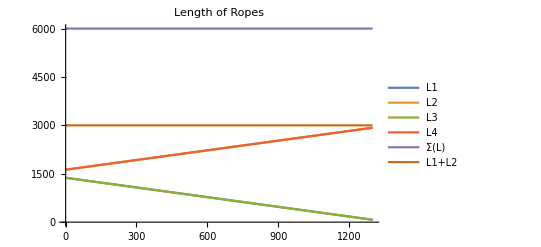

```mathematica
Animate[Graphics3D[{
OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[1]]}, Axes-> True, AxesLabel->{"X","Y", "Z"}
],{y,0,1300,Appearance->"Labeled"}, AnimationRunning->False, AnimationDirection->ForwardBackward]
Plot[
{
OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[2]],OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[3]],OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[4]],OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[5]],OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[6]],
OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[2]]+OneDoFCabledFrameContinuousMotion[y,3000,1000,100,1500][[3]]
},{y,0,1300},PlotLegends->{"L1", "L2", "L3", "L4", "Σ(L)", "L1+L2"} ,PlotLabel->"Length of Ropes"]
```

```mathematica
(*
halfWorkSpaceLength = minCylinderHeight+ maxDisp + 2*barCrossSectionalWidth; 

frameOrigin = {origin[[1]] + offsetX,origin[[2]] + offsetY, origin[[3]] + offsetZ};
firstFrameBar1Points = {
{frameOrigin[[1]], frameOrigin[[2]],frameOrigin[[3]]},
{frameOrigin[[1]]+halfWorkSpaceWidth + 2 * barCrossSectionalWidth, frameOrigin[[2]]+barCrossSectionalWidth,frameOrigin[[3]]+barCrossSectionalHeight}
};

firstFrameBar2Points = {
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]]-barCrossSectionalWidth+barCrossSectionalWidth, firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength, firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar3Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[1]][[3]]},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]]+halfWorkSpaceLength+barCrossSectionalWidth, firstFrameBar1Points[[2]][[3]]}
};
firstFrameBar4Points = {
{firstFrameBar2Points[[1]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[1]][[2]], firstFrameBar2Points[[1]][[3]]},
{firstFrameBar2Points[[2]][[1]]-halfWorkSpaceWidth-barCrossSectionalWidth, firstFrameBar2Points[[2]][[2]], firstFrameBar2Points[[2]][[3]]}
};
firstFrameBar5Points = {
{firstFrameBar1Points[[1]][[1]], firstFrameBar1Points[[1]][[2]], firstFrameBar1Points[[1]][[3]]+barCrossSectionalHeight},
{firstFrameBar1Points[[2]][[1]], firstFrameBar1Points[[2]][[2]], firstFrameBar1Points[[2]][[3]]+barCrossSectionalHeight}
};
firstFrameBar6Points = {
{firstFrameBar5Points[[1]][[1]], firstFrameBar5Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[1]][[3]]},
{firstFrameBar5Points[[2]][[1]], firstFrameBar5Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar5Points[[2]][[3]]}
};
firstFrameOuterCylinder1Points = {
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight},
{firstFrameBar6Points[[1]][[1]]+ 1/2*barCrossSectionalWidth, firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+outerCylinderHeight, firstFrameBar6Points[[1]][[3]]+ 1/2*barCrossSectionalHeight}
};
firstFrameOuterCylinder2Points = {
{firstFrameOuterCylinder1Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[1]][[2]], firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder1Points[[2]][[2]], firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder1Points = {
{firstFrameOuterCylinder1Points[[1]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y, firstFrameOuterCylinder1Points[[1]][[3]]},
{firstFrameOuterCylinder1Points[[2]][[1]], firstFrameOuterCylinder1Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder1Points[[2]][[3]]}
};
firstFrameInnerCylinder2Points = {
{firstFrameOuterCylinder2Points[[1]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y, firstFrameOuterCylinder2Points[[1]][[3]]},
{firstFrameOuterCylinder2Points[[2]][[1]], firstFrameOuterCylinder2Points[[1]][[2]]+y+minCylinderHeight, firstFrameOuterCylinder2Points[[2]][[3]]}
};
firstFrameBar7Points = {
{firstFrameBar6Points[[1]][[1]], firstFrameBar6Points[[1]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[1]][[3]]},
{firstFrameBar6Points[[2]][[1]], firstFrameBar6Points[[2]][[2]]+barCrossSectionalWidth+y+minCylinderHeight, firstFrameBar6Points[[2]][[3]]}
};
firstFrameBar8Points = {
{firstFrameBar7Points[[1]][[1]], firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[3]]},
{firstFrameBar7Points[[1]][[1]]+barCrossSectionalWidth, firstFrameBar7Points[[1]][[2]]+barCrossSectionalWidth+halfWorkSpaceLength, firstFrameBar7Points[[1]][[3]]+barCrossSectionalHeight}
};
firstFrameBar9Points = {
{firstFrameBar8Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[1]][[2]], firstFrameBar8Points[[1]][[3]]},
{firstFrameBar8Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]}
};
firstFrameBar10Points = {
{firstFrameBar8Points[[2]][[1]]-barCrossSectionalWidth, firstFrameBar8Points[[2]][[2]], firstFrameBar8Points[[2]][[3]]-barCrossSectionalHeight},
{firstFrameBar9Points[[2]][[1]], firstFrameBar9Points[[2]][[2]]+barCrossSectionalWidth, firstFrameBar9Points[[2]][[3]]}
};
firstFrameBar11Points = {
{firstFrameBar10Points[[1]][[1]], firstFrameBar10Points[[1]][[2]], firstFrameBar10Points[[1]][[3]]-barCrossSectionalHeight},
{firstFrameBar10Points[[2]][[1]], firstFrameBar10Points[[2]][[2]], firstFrameBar10Points[[2]][[3]]-barCrossSectionalHeight}
};
firstFrameBar12Points = {
{firstFrameBar11Points[[1]][[1]], firstFrameBar11Points[[1]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[1]][[3]]},
{firstFrameBar11Points[[2]][[1]], firstFrameBar11Points[[2]][[2]]-barCrossSectionalWidth, firstFrameBar11Points[[2]][[3]]}
};
firstFrameOuterCylinder3Points = {
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]], firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2},
{firstFrameBar12Points[[1]][[1]]+barCrossSectionalWidth/2, firstFrameBar12Points[[1]][[2]]-outerCylinderHeight, firstFrameBar12Points[[1]][[3]]+barCrossSectionalHeight/2}
};
firstFrameOuterCylinder4Points = {
{firstFrameOuterCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[1]][[2]], firstFrameOuterCylinder3Points[[1]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]] +halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameOuterCylinder3Points[[2]][[2]], firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder3Points = {
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y, firstFrameOuterCylinder3Points[[2]][[3]]},
{firstFrameOuterCylinder3Points[[2]][[1]], firstFrameOuterCylinder3Points[[1]][[2]]-+y-minCylinderHeight, firstFrameOuterCylinder3Points[[2]][[3]]}
};
firstFrameInnerCylinder4Points = {
{firstFrameInnerCylinder3Points[[1]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[1]][[2]], firstFrameInnerCylinder3Points[[1]][[3]]},
{firstFrameInnerCylinder3Points[[2]][[1]]+halfWorkSpaceWidth+barCrossSectionalWidth, firstFrameInnerCylinder3Points[[2]][[2]], firstFrameInnerCylinder3Points[[2]][[3]]}
};

{
Line[{{0,0,0}, {0, ySystem,0}}],
Cuboid[firstFrameBar1Points[[1]],firstFrameBar1Points[[2]]]
,
Cuboid[firstFrameBar2Points[[1]],firstFrameBar2Points[[2]]],
Cuboid[firstFrameBar3Points[[1]],firstFrameBar3Points[[2]]],
Cuboid[firstFrameBar4Points[[1]],firstFrameBar4Points[[2]]],
Cuboid[firstFrameBar5Points[[1]],firstFrameBar5Points[[2]]],
Cuboid[firstFrameBar6Points[[1]],firstFrameBar6Points[[2]]],
Cylinder[firstFrameOuterCylinder1Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder2Points, outerCylinderDia/2],
Cyan,
Cylinder[firstFrameInnerCylinder1Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder2Points, innerCylinderDia/2],
Cuboid[firstFrameBar7Points[[1]],firstFrameBar7Points[[2]]],
Orange,
Cuboid[firstFrameBar8Points[[1]],firstFrameBar8Points[[2]]],
Cuboid[firstFrameBar9Points[[1]],firstFrameBar9Points[[2]]],
Cuboid[firstFrameBar10Points[[1]],firstFrameBar10Points[[2]]],
Cuboid[firstFrameBar11Points[[1]],firstFrameBar11Points[[2]]],
Cuboid[firstFrameBar12Points[[1]],firstFrameBar12Points[[2]]],
Cyan,
Cylinder[firstFrameOuterCylinder3Points, outerCylinderDia/2],
Cylinder[firstFrameOuterCylinder4Points, outerCylinderDia/2],Pink,
Cylinder[firstFrameInnerCylinder3Points, innerCylinderDia/2],
Cylinder[firstFrameInnerCylinder4Points, innerCylinderDia/2]
}
*)
```